# Motor Physics, Template

Robert Atkinson, Maddy Nguyen, Samantha Hordyk, Cole Welch, and John Fraser
6 August 2018

This template loads in results that were computed in MotorPhysicsGears.

## Section. Administrivia

We load in the output previously computed.

```mathematica
Get[NotebookDirectory[] <> "Utilities.m"]
```

```mathematica
inputDirectory = FileNameJoin[{NotebookDirectory[],"MotorPhysicsGears.Output"}] <> $PathnameSeparator
```

C:\ftc\RobotPhysics\MotorPhysicsGears.Output\

```mathematica
Get[inputDirectory <> "ParametersUnitsAndAssumptions.m"];
$Assumptions = parameterAssumptions
```

{Bout∈ℝ,constvbat∈ℝ,constτauto∈ℝ,Jout∈ℝ,i[_]∈ℝ,vbat[_]∈ℝ,vg[_]∈ℝ,α[_]∈ℝ,θ[_]∈ℝ,τ[_]∈ℝ,τauto[_]∈ℝ,ω[_]∈ℝ,Ke>0,Kt>0,L>0,R>0,η>0,Ν>0,B≥0,J≥0,t≥0}

```mathematica
Get[inputDirectory <> "MotorModels.m"];
```

```mathematica
Get[inputDirectory <> "MotorTimeDomainFunctions.m"];
```

```mathematica
Get[inputDirectory <> "SteadyState.m"];
```

```mathematica
Get[inputDirectory <> "Misc.m"];
```

### Section.Subsection. Examples

We illustrate with examples. While computing with units is informative, computing w/o them is faster.

```mathematica
twelveVoltInput= {t  -> Quantity[t, "Seconds"], constvbat -> Quantity[12, "Volts"]} // Association // siUnits // clearUnits // N
```

<|t→t,constvbat→12.|>

```mathematica
motorWithFlywheel=addMotorLoad[motorParameters["AM 60 A"],flywheel[Quantity[3,"kg"],Quantity[8,"cm"]]]//siUnits//clearUnits//N
```

<|R→3.3,L→0.000694,Ke→0.0177667,Kt→0.0177667,J→0.00001041,B→0.033,Ν→60.,η→0.9,Jout→0.0096,Bout→0.,constτauto→0.|>

{{1.9521+2.14683 ⅇ^(-4740.08 t)-4.09893 ⅇ^(-2482.63 t)},{1.9521+2.14683 ⅇ^(-4740.08 t)-4.09893 ⅇ^(-2482.63 t)}}

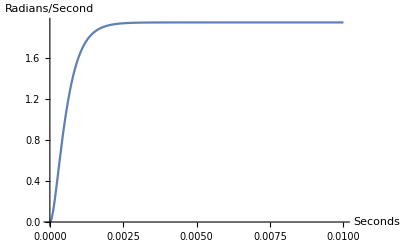

```mathematica
{ignored,vel}=applyTimeFunction[motorVelocity,motorWithFlywheel,twelveVoltInput,t]
Plot[vel,{t,0,.01},AxesLabel->{"Seconds",HoldForm[Radians/Second]},PlotRange->All,AxesOrigin->{0,0}]
```

## Section. Revision History

2018.08.06 Created template